```mathematica
L1 = {{-Subscript[k, 0]-π/Subscript[T, 2]-I π J,Subscript[k, 0]},{Subscript[k, 0],-Subscript[k, 0]-π/Subscript[T, 2]+I π J}}
```

{{-ⅈ J π-k_0-π/T_2,k_0},{k_0,ⅈ J π-k_0-π/T_2}}

```mathematica
L2 ={{-3 Subscript[k, 0]-π/Subscript[T, 2]-3I π J,3 Subscript[k, 0],0,0},
{3 Subscript[k, 0],-7 Subscript[k, 0]-π/Subscript[T, 2]-I π J, 4 Subscript[k, 0],0},
{0,4 Subscript[k, 0],-7 Subscript[k, 0]-π/Subscript[T, 2]+I π J,3 Subscript[k, 0]},
{0,0,3 Subscript[k, 0],-3 Subscript[k, 0]-π/Subscript[T, 2]+3I π J}}
```

{{-3 ⅈ J π-3 k_0-π/T_2,3 k_0,0,0},{3 k_0,-ⅈ J π-7 k_0-π/T_2,4 k_0,0},{0,4 k_0,ⅈ J π-7 k_0-π/T_2,3 k_0},{0,0,3 k_0,3 ⅈ J π-3 k_0-π/T_2}}

```mathematica
U1=FullSimplify[MatrixExp[L1 Abs[t]],{Subscript[T, 2]>0, Subscript[T, 2]∈ Reals,Subscript[k, 0]>0, Subscript[k, 0]∈ Reals}]
```

{{ⅇ^(-Abs[t] (k_0+π/T_2)) (Cosh[Abs[t] √(-J^2 π^2+k_0^2)]-(ⅈ J π Sinh[Abs[t] √(-J^2 π^2+k_0^2)])/(√(-J^2 π^2+k_0^2))),(ⅇ^(-Abs[t] (k_0+π/T_2)) Sinh[Abs[t] √(-J^2 π^2+k_0^2)] k_0)/(√(-J^2 π^2+k_0^2))},{(ⅇ^(-Abs[t] (k_0+π/T_2)) Sinh[Abs[t] √(-J^2 π^2+k_0^2)] k_0)/(√(-J^2 π^2+k_0^2)),ⅇ^(-Abs[t] (k_0+π/T_2)) (Cosh[Abs[t] √(-J^2 π^2+k_0^2)]+(ⅈ J π Sinh[Abs[t] √(-J^2 π^2+k_0^2)])/(√(-J^2 π^2+k_0^2)))}}

```mathematica
U2=FullSimplify[MatrixExp[L2 Abs[t]],{Subscript[T, 2]>0, Subscript[T, 2]∈ Reals,Subscript[k, 0]>0, Subscript[k, 0]∈ Reals}];
```

```mathematica
signal1= Total[U1 . {2,2}]
```

(4 ⅇ^(-Abs[t] (k_0+π/T_2)) Sinh[Abs[t] √(-J^2 π^2+k_0^2)] k_0)/(√(-J^2 π^2+k_0^2))+2 ⅇ^(-Abs[t] (k_0+π/T_2)) (Cosh[Abs[t] √(-J^2 π^2+k_0^2)]-(ⅈ J π Sinh[Abs[t] √(-J^2 π^2+k_0^2)])/(√(-J^2 π^2+k_0^2)))+2 ⅇ^(-Abs[t] (k_0+π/T_2)) (Cosh[Abs[t] √(-J^2 π^2+k_0^2)]+(ⅈ J π Sinh[Abs[t] √(-J^2 π^2+k_0^2)])/(√(-J^2 π^2+k_0^2)))

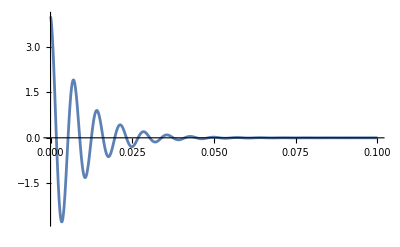

```mathematica
Plot[signal1//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 1/1000, J-> 280},{t,0,0.1},PlotRange->All]
```

```mathematica
signal2= Total[U2 . {1,1,1,1}];
```

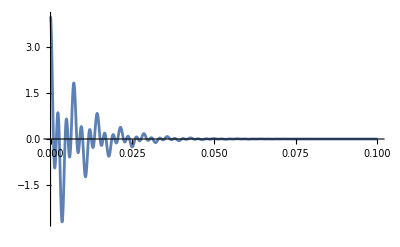

```mathematica
Plot[Simplify[N[signal2//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 1, J-> 280}]],{t,0,0.1},PlotRange->All]
```

### k_0=1

```mathematica
spec1=FourierTransform[signal1//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 1, J-> 280},t,ω,FourierParameters->{1,-1}]
```

(2400 π (43536 π+715600 π^2+9 (4+ω^2)))/(858720000 π^3+512083360000 π^4+10800 π ω^2+81 ω^2 (4+ω^2)-7200 π^2 (-50+1739 ω^2))

```mathematica
spec2=FourierTransform[Simplify[N[signal2//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 1, J-> 280}]],t,ω,FourierParameters->{1,-1}]
```

((9.0184×10^110-3.631×10^125 ⅈ)-(0.+2.24424×10^119 ⅈ) ω^2+(3.41758×10^98+5.934×10^112 ⅈ) ω^4-(3.66666×10^91+1.57915×10^106 ⅈ) ω^6)/((1.92393×10^112-5.67004×10^128 ⅈ)+(7.3392×10^106+1.55853×10^123 ⅈ) ω^2-(1.7498×10^100+1.32792×10^117 ⅈ) ω^4+(5.21481×10^92+2.908×10^110 ⅈ) ω^6-(0.+1.88497×10^103 ⅈ) ω^8)

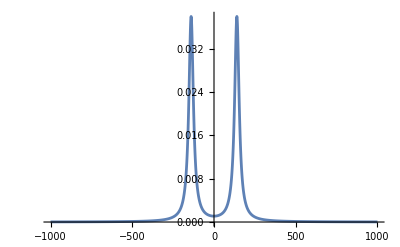

```mathematica
Plot[spec1/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

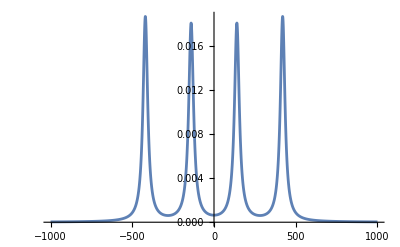

```mathematica
Plot[spec2/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

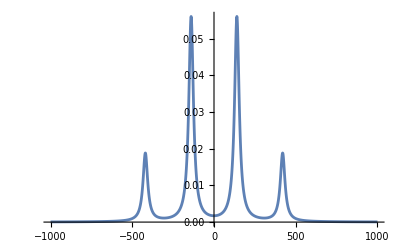

```mathematica
Plot[(spec1+spec2)/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

### k_0=100

```mathematica
spec1a=FourierTransform[signal1//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 100, J-> 280},t,ω,FourierParameters->{1,-1}]
```

(2400 π (4353600 π+715600 π^2+9 (40000+ω^2)))/(85872000000 π^3+512083360000 π^4+1080000 π ω^2+81 ω^2 (40000+ω^2)-7200 π^2 (-500000+1739 ω^2))

```mathematica
spec2a=FourierTransform[Simplify[N[signal2//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 100, J-> 280}]],t,ω,FourierParameters->{1,-1}]
```

((5.47739×10^124+0. ⅈ)+(1.07188×10^118-1.28785×10^103 ⅈ) ω^2+(9.05264×10^110+7.47595×10^96 ⅈ) ω^4+(1.5576×10^104-1.14583×10^90 ⅈ) ω^6)/((1.62817×10^127-8.41718×10^111 ⅈ)-(5.08452×10^120+4.73034×10^105 ⅈ) ω^2+(9.26058×10^114+1.90957×10^99 ⅈ) ω^4-(2.44915×10^108+1.3037×10^92 ⅈ) ω^6+1.85925×10^101 ω^8)

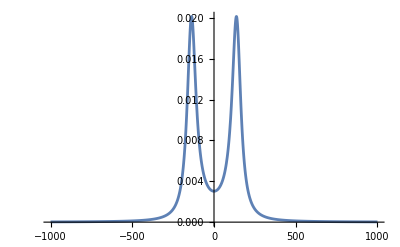

```mathematica
Plot[spec1a/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

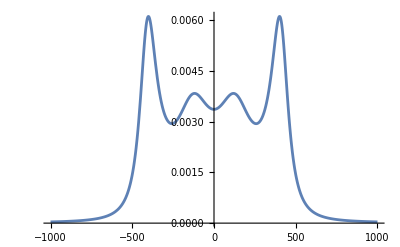

```mathematica
Plot[spec2a/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

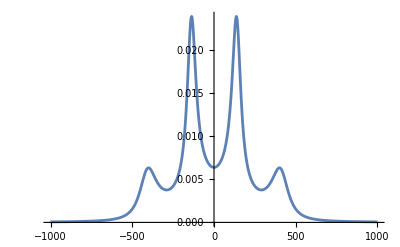

```mathematica
Plot[(spec1a+spec2a)/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

### k_0=200

```mathematica
spec1b=FourierTransform[signal1//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 200, J-> 280},t,ω,FourierParameters->{1,-1}]
```

(2400 π (8707200 π+715600 π^2+9 (160000+ω^2)))/(171744000000 π^3+512083360000 π^4+2160000 π ω^2+81 ω^2 (160000+ω^2)-7200 π^2 (-2000000+1739 ω^2))

```mathematica
spec2b=FourierTransform[Simplify[N[signal2//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 200, J-> 280}]],t,ω,FourierParameters->{1,-1}]
```

((5.17936×10^124-5.87136×10^108 ⅈ)+(7.51717×10^117-5.59936×10^101 ⅈ) ω^2+(6.41151×10^110+4.00498×10^95 ⅈ) ω^4+(3.34983×10^103-4.7743×10^88 ⅈ) ω^6)/((1.43252×10^127+1.20245×10^111 ⅈ)+(3.24386×10^120+0. ⅈ) ω^2+(1.05834×10^113+0. ⅈ) ω^4-(2.89253×10^107+0. ⅈ) ω^6+3.99856×10^100 ω^8)

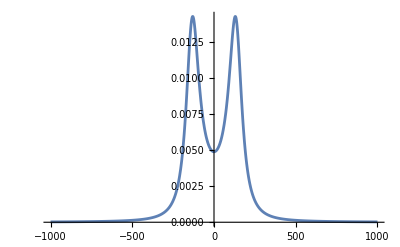

```mathematica
Plot[spec1b/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

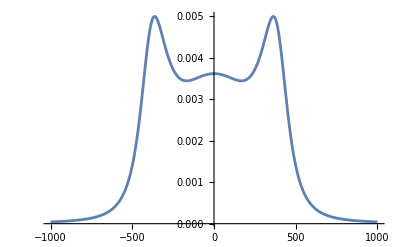

```mathematica
Plot[spec2b/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

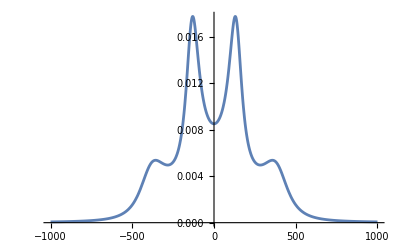

```mathematica
Plot[(spec1b+spec2b)/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

### k_0=300

```mathematica
spec1c=FourierTransform[signal1//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 300, J-> 280},t,ω,FourierParameters->{1,-1}]
```

(2400 π (13060800 π+715600 π^2+9 (360000+ω^2)))/(257616000000 π^3+512083360000 π^4+3240000 π ω^2+81 ω^2 (360000+ω^2)-7200 π^2 (-4500000+1739 ω^2))

```mathematica
spec2c=FourierTransform[Simplify[N[signal2//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 300, J-> 280}]],t,ω,FourierParameters->{1,-1}]
```

((9.94597×10^72+3.65125×10^57 ⅈ)+(1.17287×10^66+5.6999×10^50 ⅈ) ω^2+(7.26159×10^58-8.27229×10^43 ⅈ) ω^4+(2.00886×10^51-9.74499×10^36 ⅈ) ω^6)/((2.81673×10^75+0. ⅈ)+(3.43479×10^68+0. ⅈ) ω^2-(1.14086×10^62+0. ⅈ) ω^4+(5.71891×10^54+0. ⅈ) ω^6+2.39791×10^48 ω^8)

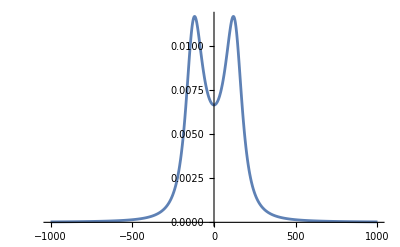

```mathematica
Plot[spec1c/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

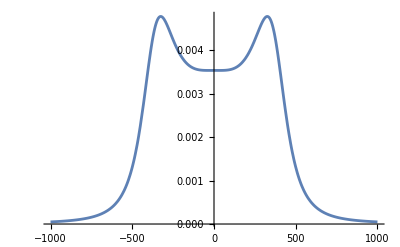

```mathematica
Plot[spec2c/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

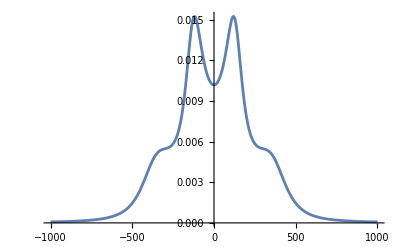

```mathematica
Plot[(spec1c+spec2c)/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

### k_0=400

```mathematica
spec1d=FourierTransform[signal1//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 400, J-> 280},t,ω,FourierParameters->{1,-1}]
```

(2400 π (17414400 π+715600 π^2+9 (640000+ω^2)))/(343488000000 π^3+512083360000 π^4+4320000 π ω^2+81 ω^2 (640000+ω^2)-7200 π^2 (-8000000+1739 ω^2))

```mathematica
spec2d=FourierTransform[Simplify[N[signal2//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 400, J-> 280}]],t,ω,FourierParameters->{1,-1}]
```

((4.07945×10^76+7.28026×10^60 ⅈ)+(3.97085×10^69-2.30003×10^54 ⅈ) ω^2+(1.78472×10^62+1.68591×10^47 ⅈ) ω^4+(3.14014×10^54+3.87621×10^40 ⅈ) ω^6)/((1.15395×10^79+0. ⅈ)+(9.96303×10^70+0. ⅈ) ω^2-(2.37146×10^65+0. ⅈ) ω^4+(5.87872×10^58+0. ⅈ) ω^6+3.74827×10^51 ω^8)

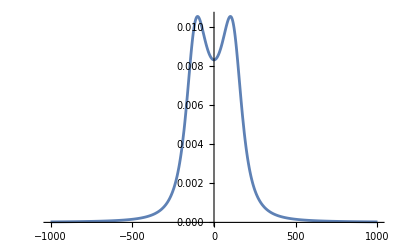

```mathematica
Plot[spec1d/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

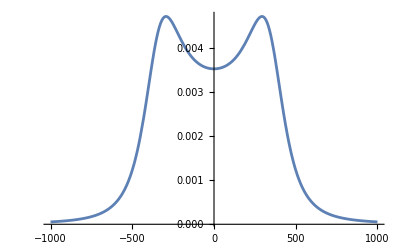

```mathematica
Plot[spec2d/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

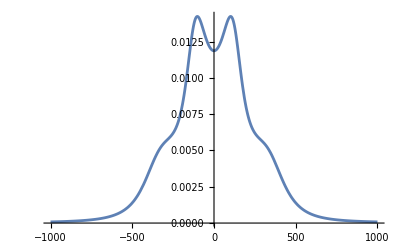

```mathematica
Plot[(spec1d+spec2d)/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

### k_0=1000

```mathematica
spec1e=FourierTransform[signal1//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 1000, J-> 280},t,ω,FourierParameters->{1,-1}]
```

(2400 π (43536000 π+715600 π^2+9 (4000000+ω^2)))/(858720000000 π^3+512083360000 π^4+10800000 π ω^2+81 ω^2 (4000000+ω^2)-7200 π^2 (-50000000+1739 ω^2))

```mathematica
spec2e=FourierTransform[Simplify[N[signal2//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 1000, J-> 280}]],t,ω,FourierParameters->{1,-1}]
```

((1.33546×10^78+1.5068×10^62 ⅈ)+(4.881×10^70-4.18152×10^55 ⅈ) ω^2+(6.16235×10^62-3.56504×10^48 ⅈ) ω^4+(2.38626×10^54-2.17089×10^40 ⅈ) ω^6)/((2.75528×10^80+0. ⅈ)-(7.05995×10^72+0. ⅈ) ω^2+(1.26995×10^67+0. ⅈ) ω^4+(4.92079×10^59+0. ⅈ) ω^6+2.84839×10^51 ω^8)

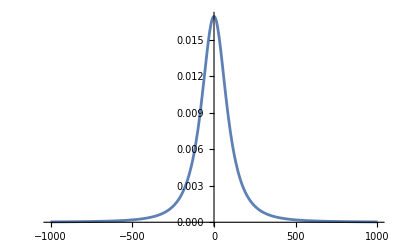

```mathematica
Plot[spec1e/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

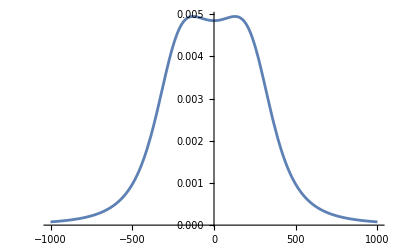

```mathematica
Plot[spec2e/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

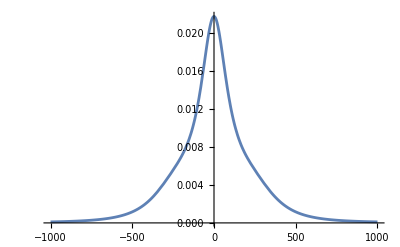

```mathematica
Plot[(spec1e+spec2e)/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

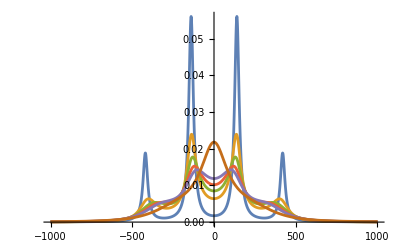

```mathematica
Plot[{(spec1+spec2)/. ω-> z*(2π),(spec1a+spec2a)/. ω-> z*(2π),(spec1b+spec2b)/. ω-> z*(2π),(spec1c+spec2c)/. ω-> z*(2π),(spec1d+spec2d)/. ω-> z*(2π),(spec1e+spec2e)/. ω-> z*(2π)},{z,-1000,1000},PlotRange->All]
```